```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jedli\OneDrive - NUS High School\Documents\Computing Studies\computed_tomography\logs

```mathematica
data=Import["masked_sinograms/data.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
fbp=Import["masked_sinograms/fbp.csv"];
fbp=Table[fbp[[i]],{i,2,Length[fbp]}];
```

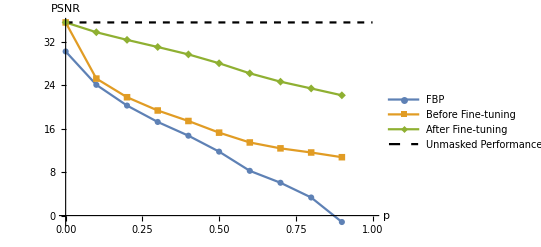

```mathematica
ListPlot[{Map[{#[[2]],#[[3]]}&,fbp],Map[{#[[2]],#[[7]]}&,data],Map[{#[[2]],#[[8]]}&,data],{{0,data[[1]][[7]]},{1,data[[1]][[7]]}}},AxesLabel->{"p","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],Directive[Black,Dashed]},PlotLegends->Placed[{"FBP","Before Fine-tuning", "After Fine-tuning","Unmasked Performance"},{0.28,0.28}],Joined->True,PlotMarkers->{Automatic,Automatic,Automatic,None},LabelStyle->Directive[FontSize->10]]
```

```mathematica
data=Import["regularly_masked_sinograms/data.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
fbp=Import["regularly_masked_sinograms/fbp.csv"];
fbp=Table[fbp[[i]],{i,2,Length[fbp]}];
```

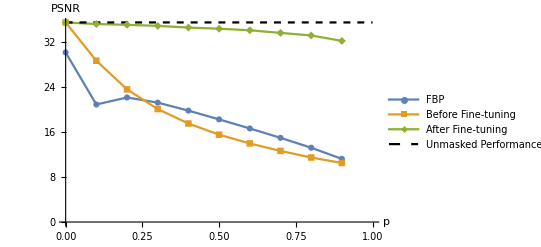

```mathematica
ListPlot[{Map[{#[[2]],#[[3]]}&,fbp],Map[{#[[2]],#[[7]]}&,data],Map[{#[[2]],#[[8]]}&,data],{{0,data[[1]][[7]]},{1,data[[1]][[7]]}}},AxesLabel->{"p","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],Directive[Black,Dashed]},PlotLegends->Placed[{"FBP","Before Fine-tuning", "After Fine-tuning","Unmasked Performance"},{0.3,0.25}],Joined->True,PlotMarkers->{Automatic,Automatic,Automatic,None},LabelStyle->Directive[FontSize->10]]
```

```mathematica
data=Import["dosage_data/data.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
fbp=Import["dosage_data/fbp.csv"];
fbp=Table[fbp[[i]],{i,2,Length[fbp]}];
```

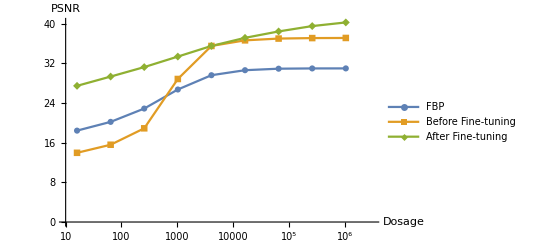

```mathematica
ListLogLinearPlot[{({#1⟦2⟧,#1⟦3⟧}&)/@fbp,({#1⟦2⟧,#1⟦7⟧}&)/@data,({#1⟦2⟧,#1⟦8⟧}&)/@data},AxesLabel->{"Dosage","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3],Directive[Black,Dashed]},PlotLegends->Placed[{"FBP","Before Fine-tuning","After Fine-tuning"},{0.75,0.25}],Joined->True,PlotMarkers->{Automatic,Automatic,Automatic,None},LabelStyle->Directive[FontSize->10],PlotRange->{{10,10^6.5},All}]
```

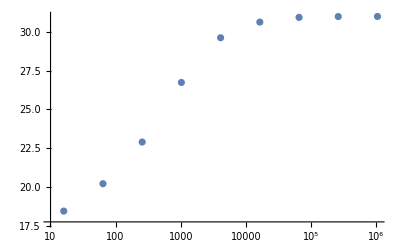

```mathematica
ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,fbp]]
```